```mathematica
ρUO2 = 10;
σsU = 8.9*^-24;
σsO = 3.75*^-24;
NA = 6.02*^23;
m238 = 238;
m235=235;
mO=16;
```

```mathematica
ΣsUO2[γ_] = (ρUO2 * NA /( (γ/(γ+1))*(m235+(m238/γ))+2*mO)) * (σsU + 2*σsO)
```

98.728/(32+((235+238/γ) γ)/(1+γ))

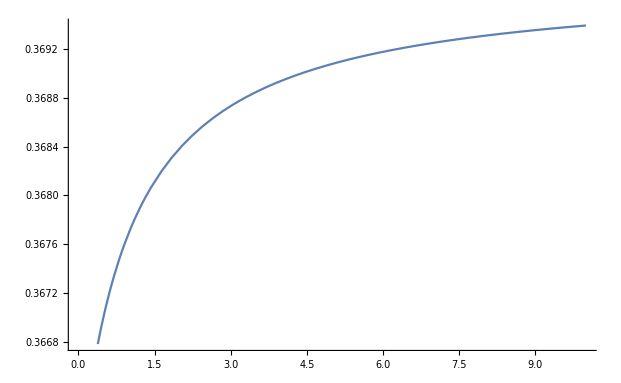

```mathematica
Plot[ΣsUO2[γ],{γ,0,10}]
```

```mathematica
γ[w_] = (w/(1-w))*(m238/m235)
```

(238 w)/(235 (1-w))

```mathematica
ΣsUO2[γ[0.05]]
```

0.365865